```mathematica
StepResponse[t_,a_,μ1_,μ2_,τ_,b_]:=a(HeavisideTheta[t-μ1](1-Exp[-(t-μ1)/τ])-HeavisideTheta[t-μ2](1-Exp[-(t-μ2)/τ]))+b
```

```mathematica
DigitizeFunction[f_,Fs_,tmax_]:=Block[{t},
Return[Table[N[{t,f[t]}],{t,0,tmax,10^6/Fs}]]
]
```

```mathematica
DigitizeFunction[f_,Fs_,tmax_,σ_]:=Block[{t},
Return[Table[N[{t,f[t]+RandomReal[NormalDistribution[0,σ]]}],{t,0,tmax,10^6/Fs}]]
]
```

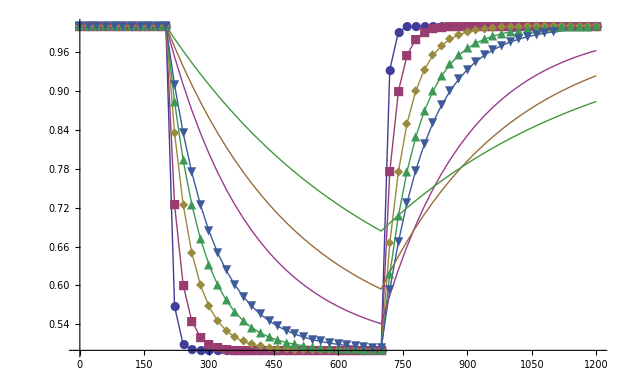

```mathematica
ListPlot[{
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,10,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,25,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,50,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,75,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,100,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,200,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,300,1]&],50000,1200,10^-9],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,500,1]&],50000,1200,10^-9]
},PlotRange->{All},PlotMarkers->{Automatic,12},Joined->True]
```

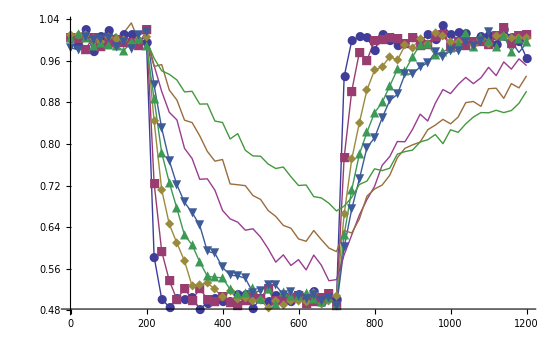

```mathematica
ListPlot[{
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,10,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,25,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,50,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,75,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,100,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,200,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,300,1]&],50000,1200,0.01],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,500,1]&],50000,1200,0.01]
},PlotRange->{All},PlotMarkers->{Automatic,12},Joined->True]
```

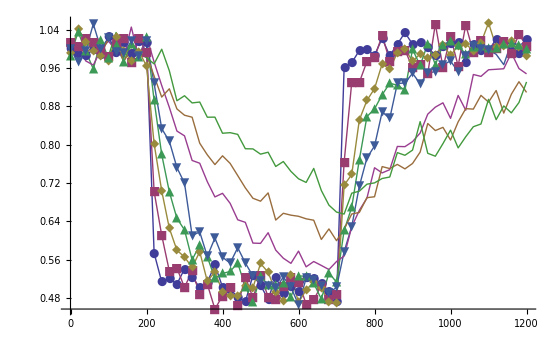

```mathematica
ListPlot[{
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,10,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,25,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,50,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,75,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,100,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,200,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,300,1]&],50000,1200,0.02],
DigitizeFunction[Evaluate[StepResponse[#,-0.5,200,700,500,1]&],50000,1200,0.02]
},PlotRange->{All},PlotMarkers->{Automatic,12},Joined->True]
```

```mathematica
WriteTestEvent[datpath_,testname_,eventparams_List]:=Block[{
csvname=datpath<>testname<>".csv",
paramsname=datpath<>testname<>".prm",
eparams={"a","tau1","tau2","mu","b","Fs","tmax","noisepct"},
a=eventparams⟦1⟧,
τ1=eventparams⟦2⟧,
τ2=eventparams⟦3⟧,
μ=eventparams⟦4⟧,
b=eventparams⟦5⟧,
Fs=eventparams⟦6⟧,
tmax=eventparams⟦7⟧,
σ=eventparams⟦8⟧
},
Export[paramsname,ToString[#⟦1⟧]<>"="<>ToString[#⟦2⟧]&/@Transpose[{eparams,CForm/@eventparams}],"CSV"];
Export[csvname, DigitizeFunction[Evaluate[StepResponse[#,a,τ1,τ2,μ,b]&],Fs,tmax,σ],"CSV"];
]
```

```mathematica
WriteTestEvent[NotebookDirectory[]<>"testdata/",#⟦1⟧,{-0.5,200,700,#⟦2⟧,1,50000,1200,10^-9}]&/@Transpose[{"test"<>ToString[#]&/@Range[1,8],{10,25,50,75,100,200,300,500}}];
```

```mathematica
WriteTestEvent[NotebookDirectory[]<>"testdata/",#⟦1⟧,{-0.5,200,700,#⟦2⟧,1,50000,1200,0.01}]&/@Transpose[{"test"<>ToString[#]&/@Range[9,16],{10,25,50,75,100,200,300,500}}];
```

```mathematica
WriteTestEvent[NotebookDirectory[]<>"testdata/",#⟦1⟧,{-0.5,200,700,#⟦2⟧,1,50000,1200,0.02}]&/@Transpose[{"test"<>ToString[#]&/@Range[17,24],{10,25,50,75,100,200,300,500}}];
```